```mathematica
css zebrafinch model;
ns is number of stressed juveniles;
nh is number of health juveniles;
NNA is number of adapted adults;
NNn is number of nonadapted adults;

ba: benefit of adaptive behavior on fecundity;
bn: benefit of non-adaptive behavior on fecundity;
pa: probability an adapted adult produces stressed offspring;
pn: probability a nonadapted adult produces stressed offspring;
vs: vitality (opposite of mortality rate) of a stresed juvenille;
vh: vitality (opposite of mortality rate) of a healthy juvenille;
vI: mortality cost of ndividual learning;
lsO : frequency of oblique learners who were stressed juveniles;
lhO : frequency of oblique learners who were healthy juveniles;


Recursions;
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs((1-lsO) vI z +lsO qO ) + nh vh((1-lhO) vI z +lhO qO );
NNn :=ns vs((1-lsO) vI (1-z)+lsO(1- qO) ) + nh vh((1-lhO) vI (1-z)+lhO(1- qO) );
qO := (1-u)(Na/(Na +Nn));
```

```mathematica
Transition Matrix;
(*leave Q in matrix below different than one up above recursions*)
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs((1-lsO) vI z +lsO Qh), vh((1-lhO) vI z +lhO Qh ), 0, 0}, {vs((1-lsO) vI (1-z)+lsO(1- Qh) ), vh((1-lhO) vI (1-z)+lhO(1- Qh) ), 0, 0}})
```

```mathematica
NN = FullSimplify[NNn + NNa];
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
solve Q-hat for common strategy;
Fasols=Solve[FFa==Fa,Fa];
```

```mathematica
PSTYLE={Directive[RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862]],Directive[RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961]],Directive[RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]],Directive[RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961]],Directive[RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253]],Directive[RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],Dashed],Directive[RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],Dashed],Directive[RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],Dashed],Directive[RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],Dashed],Directive[RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],Dashed]};
ulist={0.01,0.05,0.15, 0.25 , 0.5};
blist={1.5,2,3,5};
llsOstart=0;
llhOstart=-4 ;
imax=1500;
lhOtab=lsOtab=llhOtab=llsOtab=Table[0,{i,imax-1}];
delta=12;
llsOtab[[1]]=llsOstart;
llhOtab[[1]]=llhOstart;
```

```mathematica
For[j=1,j≤Length[blist],j++,{
For[h=1,h≤Length[ulist],h++,{
subs = {ba->blist[[j]],bn->1,z->0.8,vs->.8,vh->1,vI->0.8 ,u->ulist[[h]] , pa -> 0, pn-> 1};
test = {lsO->0 ,lsV-> 0 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2};
QHAT[LHO_,LSO_] :=Simplify[Fasols[[1,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI} /.subs];
(*isolate dominant eigenvalue*)
AA2=AA/.subs;
LL=Eigenvalues[AA2];
(*isolate Dominant eigenvalue, substitute in q-hat *)
Lambda1= Simplify[LL[[2]]/.Qh->  QHAT[LHO,LSO] ];
            softmaxsubs ={lsO -> Exp[llsO]/(1 +  Exp[llsO]) , lhO -> Exp[llhO]/(1 +  Exp[llhO]) ,LSO -> Exp[LLSO]/(1 +  Exp[LLSO]) , LHO -> Exp[LLHO]/(1 +  Exp[LLHO]) };
	  Lambda2[ llsO_, llhO_,LLHO_,LLSO_]:=Lambda1 /.softmaxsubs;

(*take partial derivatives to calculate gradient, substitute mutant for common type*)
DllsO=D[Lambda2[llsO, llhO,LLHO,LLSO],llsO]/. {LLHO -> llhO,LLSO-> llsO};
DllhO=D[Lambda2[llsO, llhO,LLHO,LLSO],llhO]/. {LLHO -> llhO,LLSO-> llsO};
(*try and graph*)

llsOtab[[1]]=llsOstart;
llhOtab[[1]]=llhOstart;


For[i=2,i<imax,i++,{
llsOtab[[i]]=llsOtab[[i-1]]  + delta DllsO/.subs/.{llsO->llsOtab[[i-1]],llhO->llhOtab[[i-1]]};
llhOtab[[i]]=llhOtab[[i-1]]  + delta DllhO/.subs/.{llsO->llsOtab[[i-1]],llhO->llhOtab[[i-1]]};
}]; 

lsOtab =Exp[llsOtab]/(1+Exp[llsOtab]);
lhOtab =Exp[llhOtab]/(1+Exp[llhOtab]);

lsOtab1=If[h==1,lsOtab,lsOtab1];
lsOtab2=If[h==2,lsOtab,lsOtab2];
lsOtab3=If[h==3,lsOtab,lsOtab3];
lsOtab4=If[h==4,lsOtab,lsOtab4];
lsOtab5=If[h==5,lsOtab,lsOtab5];
lhOtab1=If[h==1,lhOtab,lhOtab1];
lhOtab2=If[h==2,lhOtab,lhOtab2];
lhOtab3=If[h==3,lhOtab,lhOtab3];
lhOtab4=If[h==4,lhOtab,lhOtab4];
lhOtab5=If[h==5,lhOtab,lhOtab5];
}];

plotcode=ListLinePlot[{lhOtab1,lhOtab2,lhOtab3,lhOtab4,lhOtab5, lsOtab1,lsOtab2,lsOtab3,lsOtab4,lsOtab5},PlotLabels->ulist,PlotRange->{All,{0,1}},PlotStyle->PSTYLE,AxesLabel->{time, freq oblique},PlotLegends->{Placed[PointLegend[ulist],Bottom],Placed[LineLegend[{Normal,Dashed},{"healthy juv","stressed juv"}],Top]},PlotLabel->subs, ImageSize->440];

p1 = If[j≠1,p1,plotcode];
       p2 = If[j≠2,p2,plotcode];
       p3 = If[j≠3,p3,plotcode];
       p4 = If[j≠4,p4,plotcode];

}];              
Grid[{{p1,p2,p3,p4}} ]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Plots for individual Graphs,softmax;
```

ReplaceAll::reps: {Null (llsO→0),Null (llhO→-4)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::write: Tag ReplaceAll in («1»)/(2 (-0.533333+0.4 Power[«2»] Power[«2»]-0.2 Power[«2»] Power[«2»]+«9»+0.148148 Power[«2»] Power[«2»] Power[«2»] Power[«2»]) Root[Plus[«11»]&,2]+2.66667 Root[«1»&,2]^3)/.{0,0} is Protected.

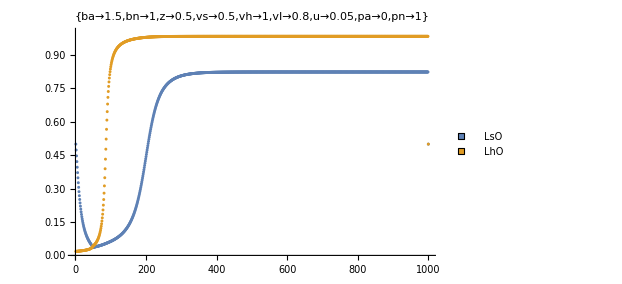

ReplaceAll::reps: {Null (llsO→0),Null (llhO→-4)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::write: Tag ReplaceAll in («1»)/(2 (-0.466667+0.4 Power[«2»] Power[«2»]-0.1 Power[«2»] Power[«2»]+«9»+0.037037 Power[«2»] Power[«2»] Power[«2»] Power[«2»]) Root[Plus[«11»]&,2]+1.33333 Root[«1»&,2]^3)/.{0,0} is Protected.

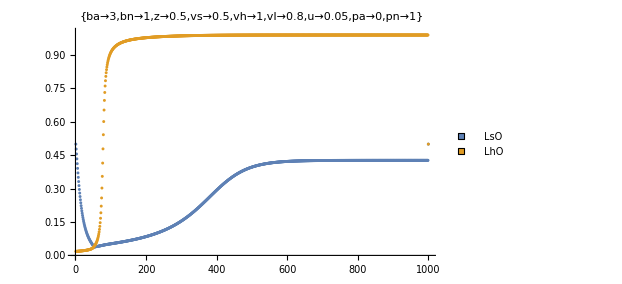

ReplaceAll::reps: {Null (llsO→0),Null (llhO→-4)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::write: Tag ReplaceAll in («1»)/(2 (-0.44+0.4 Power[«2»] Power[«2»]-0.06 Power[«2»] Power[«2»]+0.266667 Power[«2»] Power[«2»] Power[«2»]-«1»+«21» «1» «1» Power[«2»]+«1»-0.103333 Power[«2»] Power[«2»] Power[«2»] Power[«2»]-0.133333 Power[«2»] Power[«2»] Power[«2»] Power[«2»]+0.0133333 Power[«2»] Power[«2»] Power[«2»] Power[«2»]) Root[Plus[«11»]&,2]+«1»)/.{0,0} is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

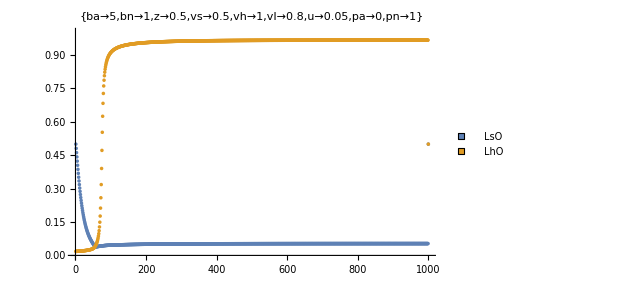

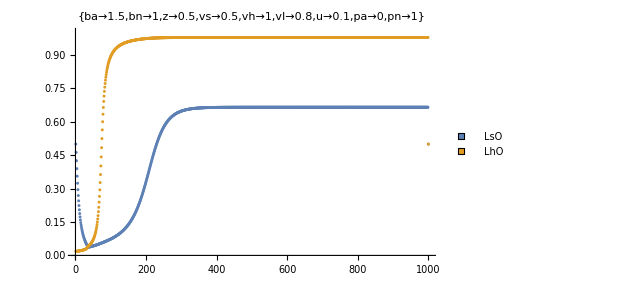

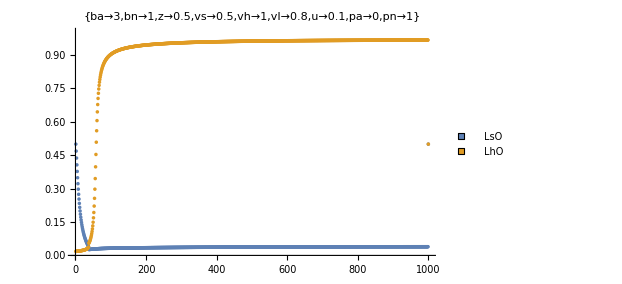

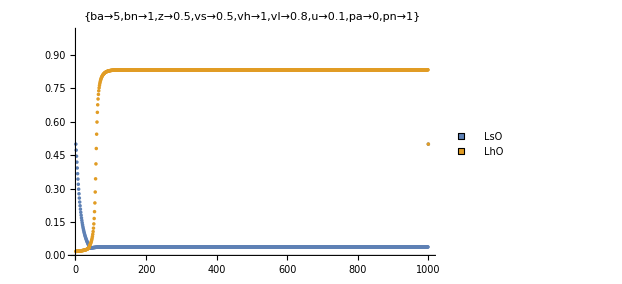

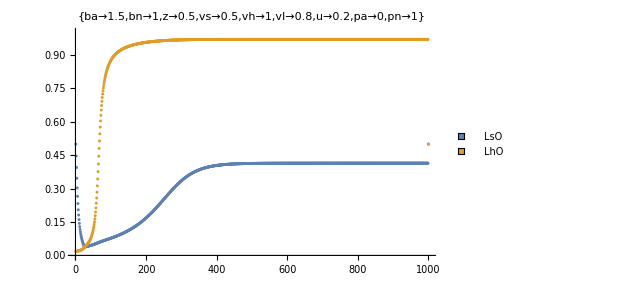

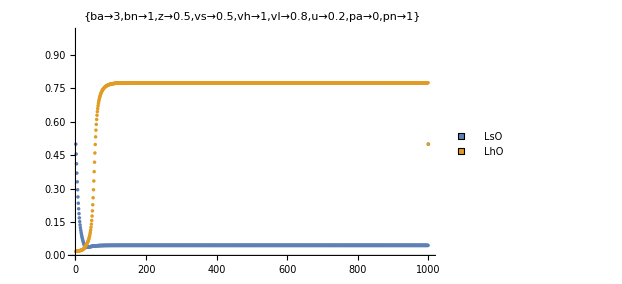

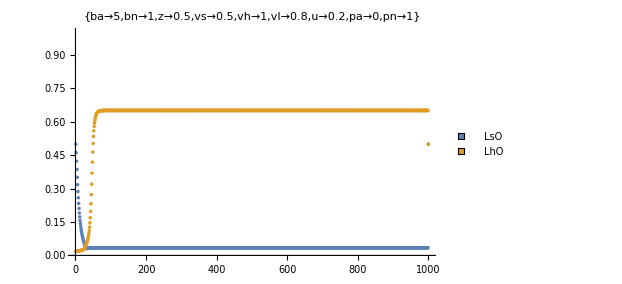

```mathematica
(* begin looping here*)
ulist={0.05,0.1, 0.2 };
blist={1.5,3,5};
lsOstart=0.5;
lhOstart=0.01;
imax=2000;
For[h=1,h≤Length[ulist],h++,{
For[j=1,j≤Length[blist],j++,{
subs = {ba->blist[[j]],bn->1,z->.5,vs->.5,vh->1,vI->.8  ,u->ulist[[h]] , pa -> 0, pn-> 1};
test = {lsO->0 ,lsV-> 0 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2};
QHAT[LHO_,LSO_] :=Simplify[Fasols[[1,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI} /.subs];
(*isolate dominant eigenvalue*)
AA2=AA/.subs;
LL=Eigenvalues[AA2];
(*isolate Dominant eigenvalue, substitute in q-hat *)
Lambda1= Simplify[LL[[2]]/.Qh->  QHAT[LHO,LSO] ];
            softmaxsubs ={lsO -> Exp[llsO]/(1 +  Exp[llsO]) , lhO -> Exp[llhO]/(1 +  Exp[llhO]) ,LSO -> Exp[LLSO]/(1 +  Exp[LLSO]) , LHO -> Exp[LLHO]/(1 +  Exp[LLHO]) };
	  Lambda2[ llsO_, llhO_,LLHO_,LLSO_]:=Lambda1 /.softmaxsubs;

(*take partial derivatives to calculate gradient, substitute mutant for common type*)
DllsO=D[Lambda2[llsO, llhO,LLHO,LLSO],llsO]/. {LLHO -> llhO,LLSO-> llsO};
DllhO=D[Lambda2[llsO, llhO,LLHO,LLSO],llhO]/. {LLHO -> llhO,LLSO-> llsO};
(*try and graph*)
llsOstart=0;
llhOstart=-4 ;
imax=1000;
llsItab=Table[0,{i,imax}];
llhItab=Table[0,{i,imax}];
llsOtab=Table[0,{i,imax}];
llhOtab=Table[0,{i,imax}];
DllsOtab=Table[0,{i,imax}];
DllhOtab=Table[0,{i,imax}];
delta=10;
llsOtab[[1]]=llsOstart;
llhOtab[[1]]=llhOstart;
DllsOtab[[1]]=DllsO/.subs/.{llsO->llsOstart,llhO->llhOstart}
DllhOtab[[1]]=DllhO/.subs/.{llsO->llsOstart,llhO->llhOstart}

For[i=2,i<imax,i++,{
DllsOtab[[i]]=DllsO/.subs/.{llsO->llsOtab[[i-1]],llhO->llhOtab[[i-1]]};
DllhOtab[[i]]=DllhO/.subs/.{llsO->llsOtab[[i-1]],llhO->llhOtab[[i-1]]};

llsOtab[[i]]=llsOtab[[i-1]]  + delta DllsOtab[[i]]/.subs/.{llsO->llsOtab[[i-1]],llhO->llhOtab[[i-1]]};
llhOtab[[i]]=llhOtab[[i-1]]  + delta DllhOtab[[i]]/.subs/.{llsO->llsOtab[[i-1]],llhO->llhOtab[[i-1]]};


}]; 

lsOtab =Exp[llsOtab]/(1+Exp[llsOtab]);
lhOtab =Exp[llhOtab]/(1+Exp[llhOtab]);

Print[ListPlot[{lsOtab,lhOtab},PlotRange->{All,{0,1}},PlotLegends->PointLegend[{LsO,LhO},LegendMarkers->Graphics[Rectangle[]]],PlotLabel->subs, ImageSize->460]];

}]
}];
```